```mathematica
FullForm[Plot[Sin[x] , {x , -π , π}]];
```

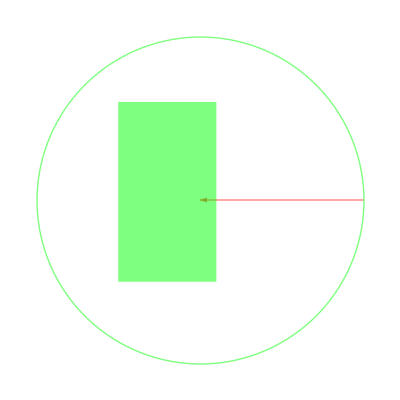

```mathematica
Graphics[
{
Green,
Opacity[0.5],
Circle[{0 , 0} , 1],
{
Red,
Arrow[{{1 , 0},{0,0}}]
},
Rectangle[{-0.5 , -0.5} , {0.1 , 0.6}]
}
]
```

```mathematica
(*The Structure of Graphics*)
```

```mathematica
a = 1.0;
b = 2.0;
a + b
```

3.

```mathematica
Hold[FullForm[a = 1.0;
b = 2.0;
a + b]]
```

Hold[CompoundExpression[Set[a,1.],Set[b,2.],Plus[a,b]]]

```mathematica
a = 1.0;
b = 2.0;
a + b;
```

```mathematica
Hold[FullForm[a = 1.0;
b = 2.0;
a + b;]]
```

Hold[CompoundExpression[Set[a,1.],Set[b,2.],Plus[a,b],Null]]

```mathematica
Module[{a , b},
a = 321.0;
b=123;
a+b
]
```

444.

```mathematica
Print[a]
```

1.

```mathematica
Print[b]
```

2.

```mathematica
Module[{a = 321.0 , b = 123},
a+b
]
```

444.

```mathematica
Print[a]
```

1.

```mathematica
Print[b]
```

2.

```mathematica
Hold[FullForm[Module[{a , b},
a = 321.0;
b=123;
a+b
]]]
```

Hold[Module[List[a,b],CompoundExpression[Set[a,321.],Set[b,123],Plus[a,b]]]]

```mathematica
a = {{a11 , a12} , {a21 , a22}};
```

```mathematica
b  ={{b11 , b12} , {b21 , b22}};
```

```mathematica
a.b
```

{{a11 b11+a12 b21,a11 b12+a12 b22},{a21 b11+a22 b21,a21 b12+a22 b22}}

```mathematica
MatrixForm[a]
```

(a11 | a12
a21 | a22)

```mathematica
MatrixForm[b]
```

(b11 | b12
b21 | b22)

```mathematica
MatrixForm[a.b]
```

(a11 b11+a12 b21 | a11 b12+a12 b22
a21 b11+a22 b21 | a21 b12+a22 b22)

```mathematica
MatrixForm[a+b]
```

(a11+b11 | a12+b12
a21+b21 | a22+b22)

```mathematica
Hold[FullForm[a.b]]
```

Hold[Dot[a,b]]

```mathematica
MatrixForm[x a]
```

(a11 x | a12 x
a21 x | a22 x)

```mathematica
?Solve
```

```mathematica
Solve[1 + 2 x + x^2 == 0 , x]
```

{{x→-1},{x→-1}}

```mathematica
(1 + x)^2//ExpandAll
```

1+2 x+x^2

```mathematica
f[f[f[x]]]
```

f[f[f[x]]]

```mathematica
Nest[f , x , 3]
```

f[f[f[x]]]

```mathematica
Nest[f , x , 0]
```

x

```mathematica
f[c_][z_]:=z +c;
```

```mathematica
f[1]
```

f[1]

```mathematica
g = f[1];
```

```mathematica
g[2]
```

3

```mathematica
h = f[2];
```

```mathematica
h[2]
```

4

```mathematica
dodajPięć = f[5];
```

```mathematica
dodajPięć[123]
```

128

```mathematica
(*ESC + ii + ESC*)
```

```mathematica
ⅈ ⅈ
```

-1

```mathematica
x + ⅈ y
```

x+ⅈ y

```mathematica
Re[2 + 5 ⅈ]
```

2

```mathematica
Im[2 + 5 ⅈ]
```

5

```mathematica
Abs[2 + 5ⅈ]
```

√29

```mathematica
Sqrt[2^2 + 5^2]
```

√29